Вариант 10

```mathematica
sys={y,-Sin[a*x]+b*y(1-x^2)};
vars={x,y};
```

Задание 1

```mathematica
points=Reduce[{sys[[1]]==0,sys[[2]]==0},vars]
```

C[1]∈Integers&&((a≠0&&(x==(2 π C[1])/a||x==(π+2 π C[1])/a))||a==0)&&y==0

Задание 2

```mathematica
Manipulate[StreamPlot[{y,-Sin[a*x]+b*y(1-x^2)},{x,-3,3},{y,-3,3}],{a,-3,3},{b,-3,3}]
```

Задание 3

```mathematica
Jac={{D[sys[[1]],x],D[sys[[1]],y]},{D[sys[[2]],x],D[sys[[2]],y]}}
```

{{0,1},{-2 b x y-a Cos[a x],b (1-x^2)}}

```mathematica
lambdas=Eigenvalues[Jac]/.{x->0,y->0}
```

{1/2 (b-√(-4 a+b^2)),1/2 (b+√(-4 a+b^2))}

```mathematica
Manipulate[{N[1/2 (a-√(-4+(-a-b)^2)+b)],N[1/2 (a+√(-4+(-a-b)^2)+b)]},{a,-5,5},{b,-5,5}]
```

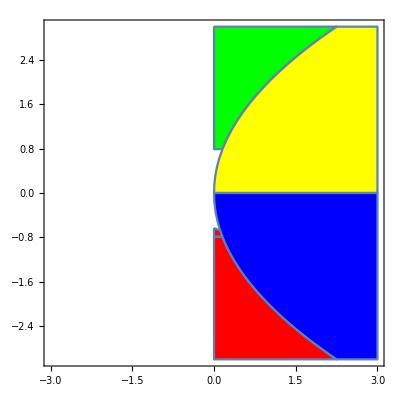

```mathematica
abmin=-3;
abmax=3;
g1=RegionPlot[Im[lambdas[[1]]]==0&&lambdas[[1]]<0&&lambdas[[2]]<0,{a,abmin,abmax},{b,abmin,abmax},PlotStyle->Red];
g2=RegionPlot[Im[lambdas[[1]]]==0&&lambdas[[1]]>0&&lambdas[[2]]>0,{a,abmin,abmax},{b,abmin,abmax},PlotStyle->Green];
g3=RegionPlot[Im[lambdas[[1]]]!=0&&Re[lambdas[[1]]]<0,{a,abmin,abmax},{b,abmin,abmax},PlotStyle->Blue];
g4=RegionPlot[Im[lambdas[[1]]]!=0&&Re[lambdas[[1]]]>0,{a,abmin,abmax},{b,abmin,abmax},PlotStyle->Yellow];
g5=RegionPlot[Re[lambdas[[1]]]==0,{a,abmin,abmax},{b,abmin,abmax},PlotStyle->Black];
Show[g1,g2,g3,g4,g5]
```

Задание 4

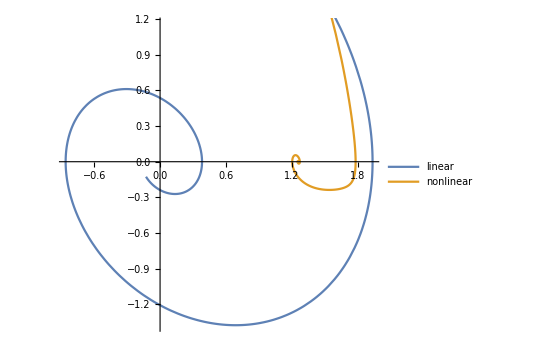

```mathematica
tmax4=10;
linsys={Jac[[1,1]]*ξ+Jac[[1,2]]*η,Jac[[2,1]]*ξ+Jac[[2,2]]*η}/.{x->0,y->0,ξ->ξ[t],η->η[t]};
lin=DSolve[{ξ'[t]==η[t],η'[t]==(a+b)* η[t]-ξ[t],ξ[0]==1,η[0]==2},{ξ,η},{t,0,tmax4}]/.{a->-2.5,b->2};
nonlin=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==1,y[0]==2}/.{a->-2.5,b->2},{x,y},{t,0,tmax4}];
ParametricPlot[{{ξ[t],η[t]}/.lin,{x[t],y[t]}/.nonlin},{t,0,tmax4},PlotLegends->{"linear","nonlinear"}]
```

```mathematica
(*задание 5*)
```

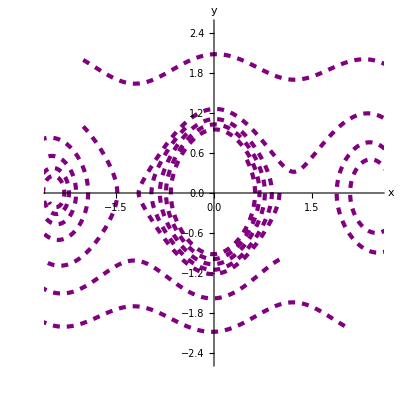

```mathematica
sol1=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==-2,y[0]==2},{x,y},{t,0,20}]/.{a->2.58,b->0.04};
sol2=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0.5,y[0]==0.5},{x,y},{t,0,20}]/.{a->2.58,b->0.04};
sol3=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==2,y[0]==-2},{x,y},{t,0,20}]/.{a->2.58,b->0.04};
sol4=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==1,y[0]==-1},{x,y},{t,0,20}]/.{a->2.58,b->0.04};sol5=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==-2,y[0]==1},{x,y},{t,0,20}]/.{a->2.58,b->0.04};
sol6=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==1,y[0]==0},{x,y},{t,0,20}]/.{a->2.58,b->0.04};
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol1],Evaluate[{x[t],y[t]}/.sol2],Evaluate[{x[t],y[t]}/.sol3],Evaluate[{x[t],y[t]}/.sol4],Evaluate[{x[t],y[t]}/.sol5],Evaluate[{x[t],y[t]}/.sol6]},{t,0,20}, PlotRange->{-2.5,2.5},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
```

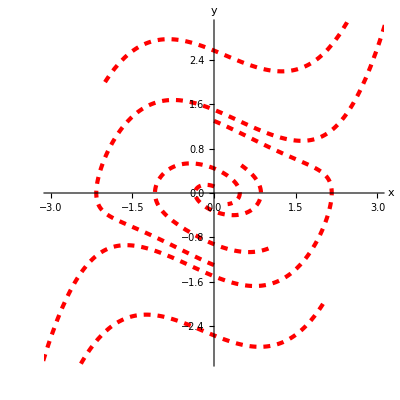

```mathematica
sol1n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==-2,y[0]==2},{x,y},{t,0,2}]/.{a->0.4,b->-0.4};
sol2n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0.5,y[0]==0.5},{x,y},{t,0,10}]/.{a->0.4,b->-0.4};
sol3n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==2,y[0]==-2},{x,y},{t,0,2}]/.{a->0.4,b->-0.4};
sol4n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==1,y[0]==-1},{x,y},{t,0,10}]/.{a->0.4,b->-0.4};sol5n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0,y[0]==-1.3},{x,y},{t,0,8}]/.{a->0.4,b->-0.4};
sol6n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0,y[0]==1.3},{x,y},{t,0,8}]/.{a->0.4,b->-0.4};
Show[ParametricPlot[{Evaluate[{x[t],y[t]}/.sol1n]},{t,0,2},PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"},PlotRange->{-3,3}],ParametricPlot[{Evaluate[{x[t],y[t]}/.sol3n]},{t,0,10},PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.sol4n]},{t,0,10},PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.sol5n]},{t,0,8},PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.sol6n]},{t,0,8},PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]}],ParametricPlot[{Evaluate[{x[t],y[t]}/.sol2n]},{t,0,10},PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]}]]
```

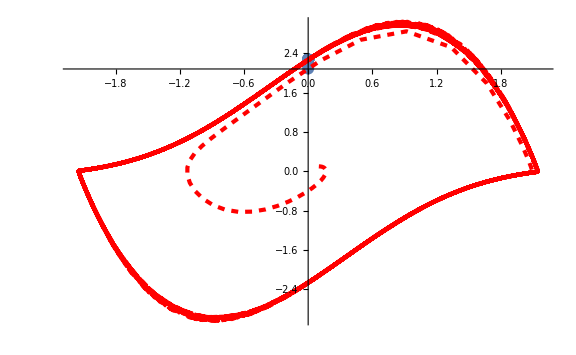

25.8133

```mathematica
sol11=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0.1,y[0]==0.1},{x,y},{t,0,500}]/.{a->1.44,b->1.44};

k=0;
a=1.44;
b=1.44;
data=Block[{},Reap[NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0.1,y[0]==0.1,WhenEvent[{x[t]==0 &&x'[t]>0},{Sow[{x[t],y[t]}],k++,time[k]=t}]},{},{t,0,500},MaxSteps->∞]]][[-1,1]];
Show[ListPlot[data,ImageSize->Large,PlotRange->{{-3,3},All},PlotStyle->PointSize[0.015]],ParametricPlot[{Evaluate[{x[t],y[t]}/.sol11]},{t,0,500}, PlotRange->All,PlotStyle->{Directive[Red,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}],PlotRange->{{-2.2,2.2},{-3,3}}]
qw=Table[{time[i],data[[i,2]]},{i,1,k}];
For[i=5,i≤25,i++,Tcycle[i]=time[i+1]-time[i]]
Tcycle[10]
ListPlot[qw,AxesLabel->{"t","y"},PlotRange->All,PlotStyle->{Directive[Purple,PointSize[0.015]]}]
```

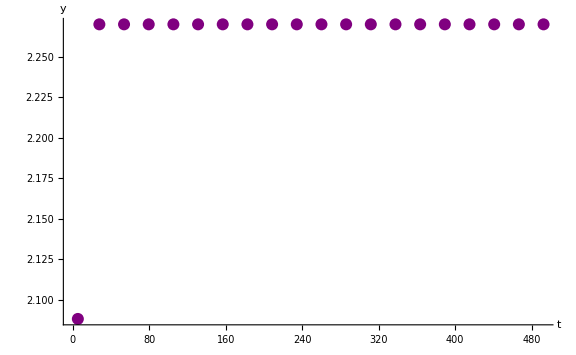

5.5 алгоритм Эно

```mathematica
a=1.44;
b=1.44;
f1[x_,y_]=y;
f2[x_,y_]=-Sin[a*x[t]]+b*y[t]*(1-x[t]^2);
S[x_]=x;
H[x_,y_]=D[S[x],x]*f1[x,y]
```

y

```mathematica
n=50000;
dt=0.01;
time2={};
x0=0.1;
y0=0.1;
For[i=1,i≤n,i++,
xi=x0+f1[x0,y0]*dt;
yi=y0+f2[x0,y0]*dt;
If[(S[xi]*S[x0]<0 &&(xi-x0)>0),

time2=Append[time2,{dt*(i-1)-S[x0]/H[x0,y0],y0-(S[x0]f2[x0,y0])/H[x0,y0]}]];
y0=yi;
x0=xi;
Clear[xi,yi]]
ListPlot[time2,PlotRange->All,AxesLabel->{"t","y"},PlotStyle->{Directive[Purple,PointSize[0.015]]}]
```

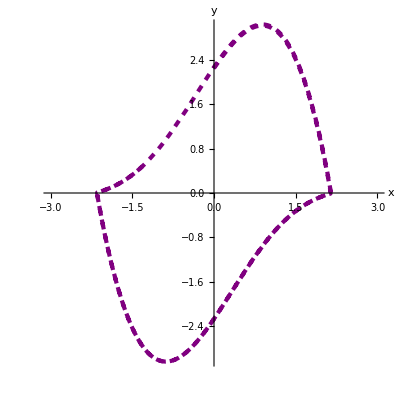

{{-1.99636,0.056591}}

```mathematica
(* задание 6*)

sol0=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0,y[0]==2.25},{x,y},{t,0,50}]/.{a->1.44,b->1.44};
ParametricPlot[Evaluate[{x[t],y[t]}/.sol0],{t,0,50}, PlotRange->{-3,3},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
dot0=Evaluate[{x[20],y[20]}/.sol0]
a=1.44;
b=1.44;
f1[x_,y_]=y;
f2[x_,y_]=-Sin[a*x[t]]+b*y[t]*(1-x[t]^2);
```

```mathematica
x0=dot0[[1,1]];
y0=dot0[[1,2]];
T=0.001;
ϵ= 0.05;
n=10000;
xi=0.03;
yi=0.04;
For[i=1,i≤n,i++,
soli[i]=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==x0,y[0]==y0},{x,y},{t,0,T}]/.{a->1.44,b->1.44};
solj[i]=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==x0+xi,y[0]==y0+yi},{x,y},{t,0,T}]/.{a->1.44,b->1.44};
doti0=Evaluate[{x[T],y[T]}/.soli[i]];
doti1=Evaluate[{x[T],y[T]}/.solj[i]];
x0=doti0[[1,1]];
y0=doti0[[1,2]];
vec=doti1-doti0;
x1=vec[[1,1]];
y1=vec[[1,2]];
xi=x1/Sqrt[x1^2+y1^2]*ϵ;
yi=y1/Sqrt[x1^2+y1^2]*ϵ;
otkl[i]=Sqrt[x1^2+y1^2];]
Λ=1/n/T*Sum[Log[otkl[i]/ϵ],{i,1,n,1}]
```

-0.0390721

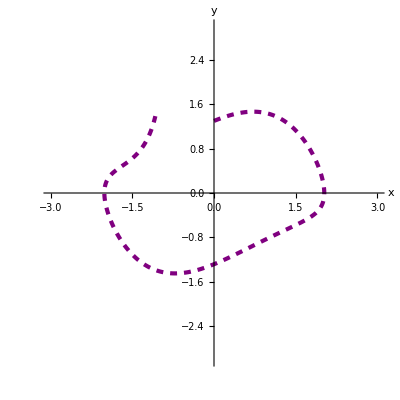

{{2.01995,0.0759881}}

```mathematica
sol6n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0,y[0]==1.3},{x,y},{t,0,8}]/.{a->0.4,b->-0.4};
ParametricPlot[Evaluate[{x[t],y[t]}/.sol6n],{t,0,10}, PlotRange->{-3,3},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
dot0=Evaluate[{x[2],y[2]}/.sol6n]
a=0.4;
b=0.4;
f1[x_,y_]=y;
f2[x_,y_]=-Sin[a*x[t]]+b*y[t]*(1-x[t]^2);
```

```mathematica
x0=dot0[[1,1]];
y0=dot0[[1,2]];
T=0.001;
ϵ= 0.05;
n=10000;
xi=0.03;
yi=0.04;
For[i=1,i≤n,i++,
soli[i]=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==x0,y[0]==y0},{x,y},{t,0,T}]/.{a->0.4,b->-0.4};
solj[i]=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==x0+xi,y[0]==y0+yi},{x,y},{t,0,T}]/.{a->0.4,b->-0.4};
doti0=Evaluate[{x[T],y[T]}/.soli[i]];
doti1=Evaluate[{x[T],y[T]}/.solj[i]];
x0=doti0[[1,1]];
y0=doti0[[1,2]];
vec=doti1-doti0;
x1=vec[[1,1]];
y1=vec[[1,2]];
xi=x1/Sqrt[x1^2+y1^2]*ϵ;
yi=y1/Sqrt[x1^2+y1^2]*ϵ;
otkl[i]=Sqrt[x1^2+y1^2];]
Λ=1/n/T*Sum[Log[otkl[i]/ϵ],{i,1,n,1}]
```

0.108863

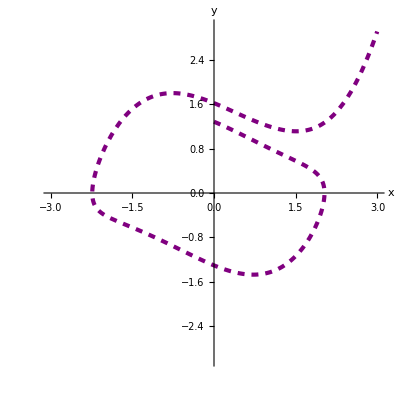

{{1.66686,0.49649}}

```mathematica
(*задание 6,5*)
sol6n=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0,y[0]==1.285},{x,y},{t,0,13}]/.{a->0.4,b->-0.4};
ParametricPlot[Evaluate[{x[t],y[t]}/.sol6n],{t,0,13}, PlotRange->{-3,3},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}]
dot0=Evaluate[{x[2],y[2]}/.sol6n]
a=0.4;
b=-0.4;
f1[x_,y_]=y;
f2[x_,y_]=-Sin[a*x[t]]+b*y[t]*(1-x[t]^2);
```

{{0.0001,0.671221},{0.0002,0.432541},{0.0003,0.38744},{0.0004,0.519707},{0.0005,0.679419},{0.0006,0.552603}}

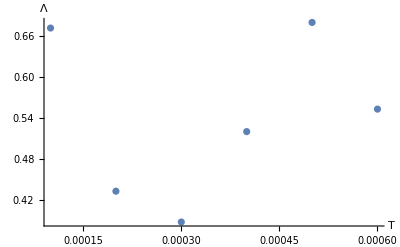

```mathematica
ew={};
n=2500;
ϵ= 0.25;
tr=6;
Do[
x0=dot0[[1,1]];
y0=dot0[[1,2]];

For[d=0,d<tr,d++,
θ=π/3*d;
xi=ϵ Cos[θ];
yi=ϵ Sin[θ];
Clear[soli,solj,doti0,doti1,otkl];
For[i=1,i≤n,i++,
soli[i]=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==x0,y[0]==y0},{x,y},{t,0,T}]/.{a->0.4,b->0.4};
solj[i]=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==x0+xi,y[0]==y0+yi},{x,y},{t,0,T}]/.{a->0.4,b->0.4};
doti0=Evaluate[{x[T],y[T]}/.soli[i]];
doti1=Evaluate[{x[T],y[T]}/.solj[i]];
x0=doti0[[1,1]];
y0=doti0[[1,2]];
vec=doti1-doti0;
x1=vec[[1,1]];
y1=vec[[1,2]];
xi=x1/Sqrt[x1^2+y1^2]*ϵ;
yi=y1/Sqrt[x1^2+y1^2]*ϵ;
otkl[i]=Sqrt[x1^2+y1^2];];
Λ1[d]=1/(n*T)*Sum[Log[otkl[i]/ϵ],{i,1,n,1}];];
Λ=Sum[Λ1[d],{d,0,tr-1,1}]/tr;
ew=Append[ew,{T,Λ}];
Print[ew];,{T,0.0001,0.0006,0.0001}]

ListPlot[ew,PlotRange->All,AxesLabel->{"T","Λ"},Joined->False]
```

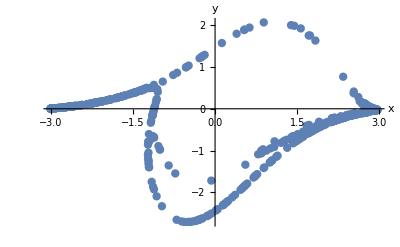

```mathematica
(*задание 7*)
n=500;
w= π/2;
A= 1;
a=1;
b=1;
T=(2π)/w;
data12=Block[{a=1,b=1},Reap[NDSolve[{x'[t]==y[t]+A*Cos[w*t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0.1,y[0]==0.1,WhenEvent[Mod[t,T]==0,Sow[{x[t],y[t]}]]},{},{t,0,T*n},MaxSteps->∞]]][[-1,1]];
sol12=NDSolve[{x'[t]==y[t]+A*Cos[w*t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2),x[0]==0.1,y[0]==0.1},{x,y},{t,0,T*n}];
qu=ListPlot[data12,PlotRange->All,PlotStyle->PointSize[0.015],AxesLabel->{"x","y"}];
er=ParametricPlot[Evaluate[{x[t],y[t]}/.sol12],{t,0,T*n},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"x","y"}];
Show[qu,PlotRange->All]
```

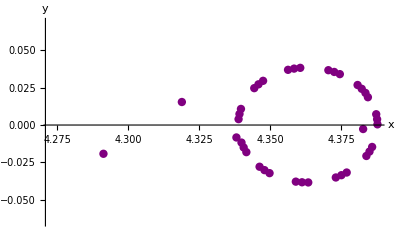

```mathematica
n=40;
A= 1;
a=1.44;
b=1.44;
Tcycle1=25.813;
data12=Block[{a=1.44,b=1.44},Reap[NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2)+A*Cos[w*t],x[0]==0.1,y[0]==0.1,WhenEvent[Mod[t,Tcycle1]==0,Sow[{x[t],y[t]}]]},{},{t,0,Tcycle1*n},MaxSteps->∞]]][[-1,1]];
sol12=NDSolve[{x'[t]==y[t],y'[t]==-Sin[a*x[t]]+b*y[t]*(1-x[t]^2)+A*Cos[w*t],x[0]==0.1,y[0]==0.1},{x,y},{t,0,Tcycle1*n}];
time3=Table[{x[Tcycle1*i]/.sol12[[1]],y[Tcycle1*i]/.sol12[[1]]},{i,1,n}];
ListPlot[time3,AxesLabel->{"x","y"},PlotStyle->{Directive[Purple,PointSize[0.015]]}]
```